{{θ→InterpolatingFunction[{{0., 60.}}, <>]}}

Single Forced Pendulum Motion:

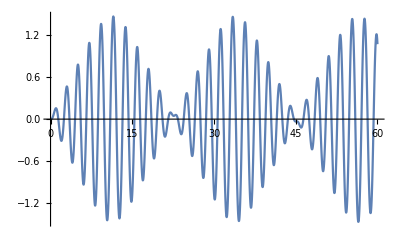

```mathematica
m=1/4;
l=1;
g=10;
ω=Pi;
A=1/10;
ℒ=1/2*m*(l^2)*(θ'[t]^2)+m*g*l*Cos[θ[t]]+1/2*m*(A^2)*(ω^2)*((Cos[ω*t])^2)+m*A*l*ω*θ'[t]*Cos[θ[t]]*Cos[ω*t];
Needs["VariationalMethods`"]
eqs=EulerEquations[ℒ,{θ[t]},t];
s=NDSolve[{eqs,θ[0]==0,θ'[0]==0},{θ},{t,0,60}]

"Single Forced Pendulum Motion:"
Plot[Evaluate[{θ[t]}/.s],{t,0,60}]
plt=Plot[-50,{x,-l-Sqrt[m],l+Sqrt[m]},PlotRange->{-l-Sqrt[m],l+Sqrt[m]}];
Animate[Show[plt,Graphics[{Line[{{A*Sin[ω*t],0},{l*Sin[θ[t]]+A*Sin[ω*t],-l*Cos[θ[t]]}}]}],Graphics[{Red,Ball[{l*Sin[θ[t]]+A*Sin[ω*t],-l*Cos[θ[t]]},Sqrt[m]/8]}],AspectRatio->Automatic]/.s,{t,0,60},AnimationRate->1, AnimationRunning->False,RefreshRate->120]
```